# Data visualisation 1st Exam

## Instructions

Fill this notebook with the Mathematica code that answers each question, and when you are done submit the notebook with your answers through MyAberdeen. You can make multiple submissions within the deadline; only the latest submission will count. The assignment is worth a total of 6 marks, and each question indicates how many points it is worth. The deadline is 25/11/2025 (Tuesday), at 23:59. Submissions after that may be accepted (up to two days after the deadline), but your marks will be reduced (two fewer marks for each day past the deadline).

## Questions

[total: 2 marks] Create a function propPlot, accepting two arguments country and property, which when called generates a line plot of the value of that property for the given country between the years of 1960 and 2022 [0.5 marks]. So for example, propPlot[“Brazil”, “GDPPerCapita”] generates the plot shown in the image below. Of course, the function should work for any choice of valid (that is, numerical) property and any country. Use CountryData to generate the data for the plot. In addition:
	
	[0.2 marks] both axes should be labeled properly, as shown in the example;
	[0.2 marks] the title should be in the form of “<property> for <country> over the years”, as shown in the example;
	[0.3 marks] the plot should have a thick dashed horizontal line at the average value of the property;
	[0.4 marks] the plot should have thin horizontal lines at the maximum and minimum values of the property;
                [0.4 marks] large black dots should be shown at the locations of the maximum and minimum (see example image below).  

Hint: you will need to eliminate missing data properly, or your plot may not work.

Answer:

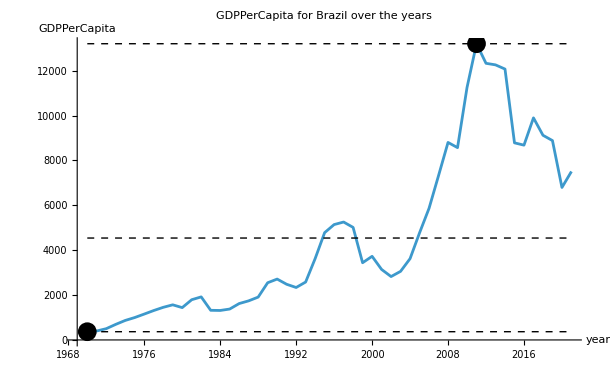

```mathematica
propPlot[country_,property_]:=Module[{Question1,dataQuestion1,cleanedDataQ1,valuesQ1,averagevalues,maximumvalues,minimumvalues,maximumpoint,minimumpoint,xAXISminimum,xAXISmaximum},
Question1=CountryData[country,{property,All}];
dataQuestion1=Normal[Question1["Path"]];
cleanedDataQ1=Map[{DateValue[#[[1]],"Year"],QuantityMagnitude[#[[2]]]}&,dataQuestion1];
cleanedDataQ1=Select[cleanedDataQ1,NumberQ[Last[#]]&&1960<=First[#]<=2022&];
valuesQ1=cleanedDataQ1[[All,2]];
averagevalues=Mean[valuesQ1];
maximumvalues=Max[valuesQ1];
minimumvalues=Min[valuesQ1];
maximumpoint=SortBy[cleanedDataQ1,Last][[-1]];
minimumpoint=SortBy[cleanedDataQ1,Last][[1]];
xAXISminimum=Min[cleanedDataQ1[[All,1]]];
xAXISmaximum=Max[cleanedDataQ1[[All,1]]];

plotLines={{Thick,Dashed,InfiniteLine[{0,averagevalues},{1,0}]},{Thin,Dashed,InfiniteLine[{0,maximumvalues},{1,0}]},{Thin,Dashed,InfiniteLine[{0,minimumvalues},{1,0}]},{Black,PointSize[Large],Point[{maximumpoint,minimumpoint}]}};

ListLinePlot[cleanedDataQ1,PlotLabel->property<>" for "<>country<>" over the years",AxesLabel->{"year",property},Epilog->{{Thick,Dashed,Line[{{xAXISminimum,averagevalues},{xAXISmaximum,averagevalues}}]},{Thin,Dashed,Line[{{xAXISminimum,maximumvalues},{xAXISmaximum,maximumvalues}}]},{Thin,Dashed,Line[{{xAXISminimum,minimumvalues},{xAXISmaximum,minimumvalues}}]},{Black,PointSize[0.022],Point[maximumpoint]},{Black,PointSize[0.022],Point[minimumpoint]}}]]

(*Testing Functions*)
propPlot["Brazil","GDPPerCapita"]
propPlot["Pakistan","GDPPerCapita"];
```

[2 marks] Create an interactive chart showing a scatter plot of the GDPPerCapita versus LiteracyFraction, using CountryData [0.2 marks]. The axes should be labeled as shown in the figure [0.1 marks]. The plot should have a slider ranging from 0 to 60000, representing a GDP threshold [0.2 marks]. In addition:

	[0.5 marks] All points with a GDPPerCapita smaller than or equal to a threshold set by the slider will have one colour, and all those with GDPPerCapita higher than the threshold will have a different colour. 
	[0.5 marks] A legend should explain the meaning of the colours, and they should mention the current value of the threshold, as shown in the image below; this value should be updated as the slider is moved.  
	[0.5 marks] Finally, each point should have a tooltip which shows when the mouse hovers over them, showing the name of the country they correspond to. 

Hint: you will need to deal with missing data; and the units CountryData adds to the quantities will get in the way, so use QuantityMagnitude judiciously.

Answer:

```mathematica
dataQuestion2=Select[Table[{CountryData[c,"Name"],QuantityMagnitude[CountryData[c,"GDPPerCapita"]],QuantityMagnitude[CountryData[c,"LiteracyFraction"]]},{c,CountryData[]}],NumericQ[#[[2]]]&&NumericQ[#[[3]]]&];

maximumvalue=60000;

Question2=Manipulate[Module[{belowData,aboveData,plotData,plotColors,legendLabels},belowData=Select[dataQuestion2,#[[2]]<=threshold&];
aboveData=Select[dataQuestion2,#[[2]]>threshold&];
plotData={};
plotColors={};
legendLabels={};

If[Length[belowData]>0,AppendTo[plotData,Table[Tooltip[{row[[3]],row[[2]]},row[[1]]],{row,belowData}]];
AppendTo[plotColors,Pink];
AppendTo[legendLabels,"GDP % less than $"<>ToString[Round[threshold]]]];

If[Length[aboveData]>=0,AppendTo[plotData,Table[Tooltip[{row[[3]],row[[2]]},row[[1]]],{row,aboveData}]];
AppendTo[plotColors, RGBColor[0.05, 0.5, 0.1]];
AppendTo[legendLabels,"GDP % greater than $"<>ToString[Round[threshold]]]];
ListPlot[plotData,PlotStyle->plotColors,PlotLegends->legendLabels,AxesLabel->{"literacy","wealth"},PlotRange->{Automatic,{0,All}}]],{{threshold,10000,"gdpThreshold"},0,maximumvalue}]
```

[2 marks] The UK House of Commons has a total of 650 seats. The main parties are: Labour, Tories, and the LibDems (short for “Liberal Democrats”). Using what you learned about graphics primitives, create a function that displays the composition of the House of Commons using one square for each seat, coloured according to each party. The function accepts 3 arguments, which are the number of seats for of the three parties (in the order Labour, Tories, and then Liberal Democrats). The remainder of the seats should be displayed as “others”. The colours of the seats should be: red for Labour, blue for Tories, yellow for the Liberal Democrats, and black for others. The seats are arranged on a grid, with 50 columns and 13 rows, with first all red seats filling the grid from left to right and top to bottom; then the Tory seats follow, then LibDem seats, and then others (see image below). There should be a title and a legend, displayed as shown in the figure below. As an example, this is what the output of the function should look like: parliament[357,200,44]. Of course, the function should work for any set of inputs, not just for the numbers in the example.

	[1.5 marks] correct number and placement of squares, with the right colour;
	[0.2 marks] correct title; 
	[0.3 marks] correct legend (colour and placement).

Answer: